```mathematica
Clear ["Global`*"]
```

```mathematica
data={
{0.96,√(0.3^2+0.09^2),√(0.3^2+0.09^2)},
{1.15,√(0.17^2+0.11^2),√(0.17^2+0.11^2)},
{0.3,√(0.4^2+0.2^2),√(0.4^2+0.3^2)},
{1.4,√(0.4^2+0.1^2),√(0.4^2+0.1^2)},
{0.5,√(0.8^2+0.1^2),√(0.6^2+0.1^2)},
{0.3,√(0.5^2+0.3^2),√(0.5^2+0.3^2)},
{2.5,√(1.3^2+0.2^2),√(1.0^2+0.1^2)},
{1.5,√(2.7^2+0.6^2),√(2.1^2+0.4^2)},
{1.4,√(0.5^2+0.2^2),√(0.5^2+0.1^2)},
{0.1,√(1.9^2+0.2^2),√(1.1^2+0.2^2)},
{1.3,√(1.7^2+0.2^2),√(1.1^2+0.1^2)},
{1.6,√(1.7^2+0.3^2),√(1.1^2+0.2^2)}
};(*table 8*)
corr=({{1, -0.06, -0.03, 0.02, 0, -0.01, 0, 0.01, 0, 0, 0.01, 0}, {-0.06, 1, -0.52, 0.13, 0.07, -0.15, 0.04, 0.05, -0.01, -0.02, -0.03, 0}, {-0.03, -0.52, 1, -0.1, -0.02, 0.09, -0.01, -0.05, -0.13, 0.03, -0.01, 0.02}, {0.02, 0.13, -0.1, 1, 0.09, -0.26, 0.05, 0.07, -0.18, -0.02, -0.04, 0.02}, {0, 0.07, -0.02, 0.09, 1, -0.12, 0.01, 0.02, -0.2, 0, -0.08, 0.02}, {-0.01, -0.15, 0.09, -0.26, -0.12, 1, -0.03, -0.45, -0.28, 0.04, -0.01, -0.04}, {0, 0.04, -0.01, 0.05, 0.01, -0.03, 1, -0.13, -0.06, -0.42, -0.04, -0.1}, {0.01, 0.05, -0.05, 0.07, 0.02, -0.45, -0.13, 1, 0.06, 0.03, -0.03, -0.11}, {0, -0.01, -0.13, -0.18, -0.2, -0.28, -0.06, 0.06, 1, -0.02, 0, 0.01}, {0, -0.02, 0.03, -0.02, 0, 0.04, -0.42, 0.03, -0.02, 1, 0.01, 0.03}, {0.01, -0.03, -0.01, -0.04, -0.08, -0.01, -0.04, -0.03, 0, 0.01, 1, -0.08}, {0, 0, 0.02, 0.02, 0.02, -0.04, -0.1, -0.11, 0.01, 0.03, -0.08, 1}});
covariance=({{0.1, 0, 0, 0, 0, 0, 0, 0.01, 0, 0, 0, 0}, {0, 0.04, -0.05, 0.01, 0.01, -0.02, 0.01, 0.02, 0, -0.01, -0.01, 0}, {0, -0.05, 0.19, -0.02, -0.01, 0.02, -0.01, -0.05, -0.03, 0.02, -0.01, 0.01}, {0, 0.01, -0.02, 0.17, 0.03, -0.06, 0.02, 0.07, -0.04, -0.01, -0.02, 0.01}, {0, 0.01, -0.01, 0.03, 0.48, -0.05, 0.01, 0.03, -0.07, 0, -0.08, 0.02}, {0, -0.02, 0.02, -0.06, -0.05, 0.32, -0.02, -0.62, -0.09, 0.03, -0.01, -0.03}, {0, 0.01, -0.01, 0.02, 0.01, -0.02, 1.41, -0.36, -0.04, -0.72, -0.06, -0.16}, {0.01, 0.02, -0.05, 0.07, 0.03, -0.62, -0.36, 5.94, 0.08, 0.11, -0.1, -0.37}, {0, 0, -0.03, -0.04, -0.07, -0.09, -0.04, 0.08, 0.29, -0.02, 0, 0.01}, {0, -0.01, 0.02, -0.01, 0, 0.03, -0.72, 0.11, -0.02, 2.07, 0.02, 0.06}, {0, -0.01, -0.01, -0.02, -0.08, -0.01, -0.06, -0.1, 0, 0.02, 1.97, -0.15}, {0, 0, 0.01, 0.01, 0.02, -0.03, -0.16, -0.37, 0.01, 0.06, -0.15, 1.99}});
```

```mathematica
SymmetricMatrixQ[covariance]
```

True

```mathematica
For[i=1,i<=12,i++,
For[j=i,j<=12,j++,
If[corr[[i,j]]≠corr[[j,i]],Print["wrong at {i,j}= {",i,",",j,"}"]]
]
]
```

```mathematica
alphaEven={0.153,0.874,0.881};
betaEven={-0.133,0.005,0.120};
diEven={0.614,2.294,0.703};
diiEven={
{0,0.08,-1.21},
{0.08,0,-1.22},
{-1.21,-1.22,0}
};
diiiEven=0.050;
alphaOdd={0.118,0.853,0.826};
betaOdd={-0.001,-0.001,0.001};
diOdd={0.572,2.022,0.644};
diiOdd={
{0,-0.010,-1.070},
{-0.010,0,-1.085},
{-1.070,-1.085,0}
};
diiiOdd=-0.060;
```

```mathematica
c={cHW,cHB,cHWB};
rule1={cHW->cHW,cHB->0,cHWB->0,cHG->0,cuH->0};
rule2={cHW->0,cHB->cHB,cHWB->0,cHG->0,cuH->0};
rule3={cHW->0,cHB->0,cHWB->cHWB,cHG->0,cuH->0};
rule4={cHW->0,cHB->0,cHWB->0,cHG->cHG,cuH->0};
rule5={cHW->0,cHB->0,cHWB->0,cHG->0,cuH->cuH};
normAcEven=alphaEven[[1]]+alphaEven[[2]]^2*(alphaEven[[3]]+Sum[diEven[[i]]*(c[[i]]+betaEven[[i]])^2,{i,1,3}]+Sum[diiEven[[i,j]]*c[[i]]*c[[j]],{i,1,3},{j,1,3}]+diiiEven*c[[1]]*c[[2]]*c[[3]])^-1//Expand;
normAcOdd=alphaOdd[[1]]+alphaOdd[[2]]^2*(alphaOdd[[3]]+Sum[diOdd[[i]]*(c[[i]]+betaOdd[[i]])^2,{i,1,3}]+Sum[diiOdd[[i,j]]*c[[i]]*c[[j]],{i,1,3},{j,1,3}]+diiiOdd*c[[1]]*c[[2]]*c[[3]])^-1//Expand;
A1Even=normAcEven/.rule1;
A2Even=normAcEven/.rule2;
A3Even=normAcEven/.rule3;
A1Odd=normAcOdd/.rule1;
A2Odd=normAcOdd/.rule2;
A3Odd=normAcOdd/.rule3;
```

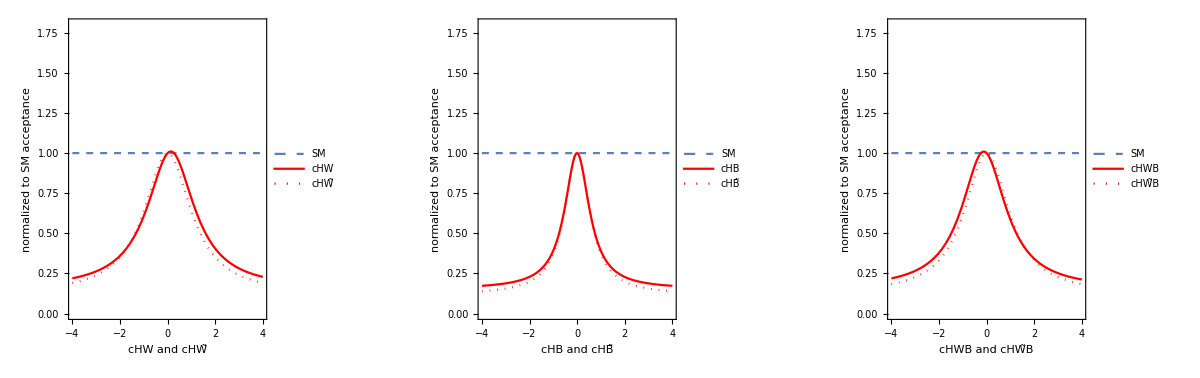

```mathematica
plot1=Plot[{1,A1Even,A1Odd},{cHW,-4,4},PlotStyle->{Dashed,Red,{Red,Dotted}},Frame->True,Axes->False,PlotRange->{{-4,4},{0,1.8}},AspectRatio->1,PlotLegends->Placed[{"SM","cHW","cHW̃"},{0.7,0.75}],FrameLabel->{"cHW and cHW̃","normalized to SM acceptance"}];
plot2=Plot[{1,A2Even,A2Odd},{cHB,-4,4},PlotStyle->{Dashed,Red,{Red,Dotted}},Frame->True,Axes->False,PlotRange->{{-4,4},{0,1.8}},AspectRatio->1,PlotLegends->Placed[{"SM","cHB","cHB̃"},{0.7,0.75}],FrameLabel->{"cHB and cHB̃","normalized to SM acceptance"}];
plot3=Plot[{1,A3Even,A3Odd},{cHWB,-4,4},PlotStyle->{Dashed,Red,{Red,Dotted}},Frame->True,Axes->False,PlotRange->{{-4,4},{0,1.8}},AspectRatio->1,PlotLegends->Placed[{"SM","cHWB","cHW̃B"},{0.7,0.75}],FrameLabel->{"cHWB and cHW̃B","normalized to SM acceptance"}];
GraphicsRow[{plot1,plot2,plot3},PlotLabel->"ABC"]
```

```mathematica
SfracEven={
1+35.8cHG+326.23 cHG^2,
1+35.33 cHG+319.05 cHG^2,
1+31.27 cHG+264.44 cHG^2,
1+29.55 cHG+236.09 cHG^2,
1+28cHG+225.53 cHG^2,
1+17.62 cHG+118.92 cHG^2,
1+17.77 cHG+162.65 cHG^2,
1+0.593cHW+0.258 cHW^2+0.019cHB+0.014 cHB^2+0.088 cHWB+0.023 cHWB^2+0.005cHW cHB+0.034 cHW cHWB+0.005cHB cHWB,
1+0.059 cHW+0.092 cHW^2+0.002 cHB+0.027 cHB^2+0.037 cHWB+0.018 cHWB^2+0.015 cHW cHB-0.016cHW cHWB-0.024 cHB cHWB,
1+0.19cHW+0.506 cHW^2-0.002cHB+0.057 cHB^2+0.042cHWB+0.048 cHWB^2+0.012cHW cHB-0.059cHW cHWB-0.028cHB cHWB,
1+0.828 cHW+0.321 cHW^2+0.035 cHB +0.013 cHB^2+0.127 cHWB+0.026 cHWB^2-0.218cHW cHB-0.155 cHW cHWB +0.02 cHB cHWB,
1+0.483 cHG+0.59 cHG^2-0.108 cuH+0.009 cuH^2-0.015cHG cuH
};
GfracEven={
1-0.199cHW+0.753 cHW^2-0.112 cHB+2.665 cHB^2+0.181 cHWB+0.76 cHWB^2-0.043cHW cHB -1.288 cHW cHWB-1.397 cHB cHWB,
1-0.054cHW +0.162 cHW^2-0.076 cHB+1.209 cHB^2+0.062cHWB+0.357 cHWB^2+1.519cHG+14.922 cHG^2+0.518 cHW cHB-0.441 cHW cHWB-1.132 cHB cHWB
};
BEven=GfracEven[[1]]/GfracEven[[2]];
```

```mathematica
func1=SfracEven[[2]]*BEven/.rule1
func2=SfracEven[[2]]*BEven*A1Even/.rule1
func3=SfracEven[[2]]/.rule1
```

(1. (1.-0.199 cHW+0.753 cHW^2))/(1.-0.054 cHW+0.162 cHW^2)

(1. (0.153+0.763876/(0.891181+0.614 (-0.133+cHW)^2)) (1.-0.199 cHW+0.753 cHW^2))/(1.-0.054 cHW+0.162 cHW^2)

1.

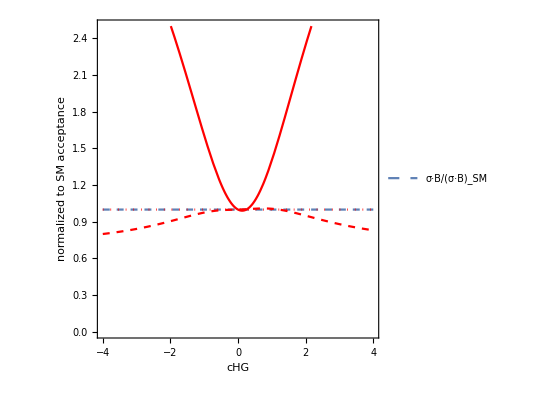

```mathematica
Plot[{1,func1,func2,func3},{cHW,-4,4},PlotStyle->{Dashed,Red,{Red,Dashed},{Red,Dotted}},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{-4,4},{0,2.5}},PlotLegends->Placed[{"σ·B/(σ·B)_SM"},{0.7,0.75}],FrameLabel->{"cHG","normalized to SM acceptance"}]
```

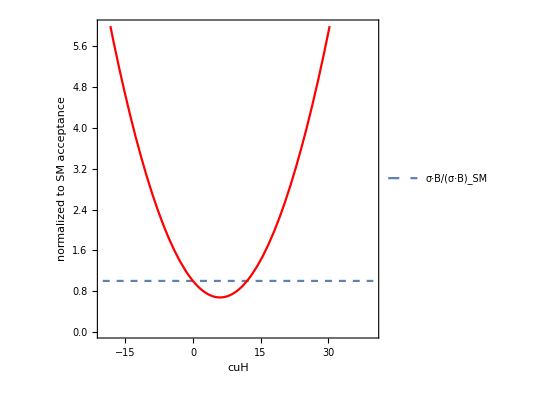

```mathematica
Plot[{1,func3},{cuH,-20,40},PlotStyle->{Dashed,Red},Frame->True,Axes->False,AspectRatio->1,PlotRange->{{-20,40},{0,6}},PlotLegends->Placed[{"σ·B/(σ·B)_SM"},{0.7,0.75}],FrameLabel->{"cuH","normalized to SM acceptance"}]
```

```mathematica
mu0=Transpose[data][[1]];
```

```mathematica
mu=SfracEven*BEven*normAcEven/.rule5;
```

```mathematica
mueff=(mu-mu0)/.cuH->x;
n=Length[data];
VGau=Table[data[[i,2]]*data[[i,3]],{i,1,n}];
VGauPrime=Table[data[[i,2]]-data[[i,3]],{i,1,n}];
```

```mathematica
PointList={};
maxL=1000;
xmax=-20;
For[y=-20,y<=30,y+=0.01,
dx=mueff/.x->y;
sym=√Abs[VGau+VGauPrime*dx];
Cov=Table[corr[[j,k]]*sym[[j]]*sym[[k]],{j,1,n},{k,1,n}];
invCov=Inverse[Cov];
(*LogL=dx.invCov.dx;*)
LogL=Sum[dx[[i]]*invCov[[i,j]]*dx[[j]],{i,1,n},{j,1,n}];
If[LogL<maxL,maxL=LogL;xmax=y];
AppendTo[PointList,{y,LogL}]
];
Print["best fit at ",xmax]
```

best fit at -5.34

```mathematica
L0=Min[Transpose[PointList][[2]]];
L2List=Transpose[PointList][[2]]-L0;
PointList2={Transpose[PointList][[1]],L2List}//Transpose;
```